```mathematica
data={{0.252501,6.007},{0.274458,5.941372},{0.287784,5.916334},{0.299207,5.910821},{0.311264,5.873631},{0.321925,5.856265},{0.332586,5.840677},{0.344453,5.823916}}
```

{{0.252501,6.007},{0.274458,5.94137},{0.287784,5.91633},{0.299207,5.91082},{0.311264,5.87363},{0.321925,5.85627},{0.332586,5.84068},{0.344453,5.82392}}

```mathematica
worig={0.015398,0.011844,0.011844,0.011844,0.012733,0.013029,0.012437,0.012140}
```

{0.015398,0.011844,0.011844,0.011844,0.012733,0.013029,0.012437,0.01214}

```mathematica
w={0.016,0.011,0.011,0.011844,0.012733,0.013029,0.012437,0.011};lm=LinearModelFit[data,x,x, Weights->1/w^2]
```

FittedModel[6.45797-1.85701 x]

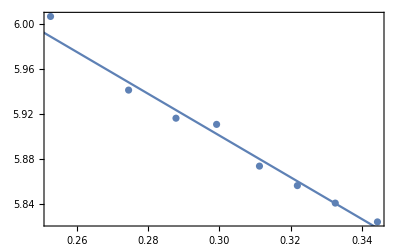

```mathematica
Show[ListPlot[data],Plot[lm[x],{x,0,5}],Frame->True]
```

```mathematica
res=lm["FitResiduals"];Total[res^2/w^2]
```

3.19027

```mathematica
6.462069079455865-1.869841517462548 *0.299
```

5.90299